```mathematica
Vn[r_] := b*r
r = Sqrt[k]*p
```

√k p

```mathematica
Vn[r]/k
```

(b p)/(√k)

```mathematica
Vn[r_] := b*r;
r = Sqrt[k]*p;
var=k;
p0=1/(4*c)^(1/3);
V[p_] := c*p+ 1/(8*p^2); 
c= 2^(7/2)/3^(1/2);
k=3;
```

```mathematica
W[n_,m_] := Which[n==0 && m==0, -1/(2*p0^2), n==0 && m==2, (D[V[p],{p,2}]/.p->p0)/Factorial[2], n ==1 && m ==1, 1/p0^3,n==1&&m==3,(D[V[p],{p,3}]/. p->p0)/Factorial[3] , m==n-2, (-1)^n*3*(n-1)/(8*p0^n),m == n, (-1)^(n+1)*(n+1)/(2*p0^(n+2)),m == n+2,(D[V[p],{p,n+2}]/.p->p0)/Factorial[n+2],True,0  ]
```

```mathematica
Cs[n_,m_]:= Cs[n,m] = Which[m>=n+2,0,m<0,0,True, -1/(2*Ds[0,1])(-2*W[2*n+1,2*m+1]+2*(m+1)*Cs[n,m+1]+2*Sum[Ds[i,j]*Cs[n-i,m+1-j],{i,1,n},{j,1,i+1}])]
```

```mathematica
Ds[n_,m_]:= Ds[n,m]= Which[m>=n+2,0,m<=0,0,n==0&& m==1, -Sqrt[2*W[0,2]],True,-1/(2*Ds[0,1])(-2*W[2*n,2*m]+(2*m+1)*Ds[n,m+1]+Sum[Ds[i,j]*Ds[n-i,m+1-j],{i,1,n-1},{j,1,i+1}] + Sum[Cs[i,j]*Cs[n-i-1,m-j],{i,0,n-1},{j,0,i+1}])]
```

```mathematica
Eminusone[n_] := Eminusone[n] = N[1/2*(-Ds[n,1]+2*W[2*n,0]-Sum[Cs[i,0]*Cs[n-i-1,0],{i,0,n-1}])*k^(-n)]
```

```mathematica
Eminusone[8]
```

$Aborted

```mathematica
N[Eminusone[6]]
```

-0.00099505

```mathematica
l = {k*V[p0]}
```

{(9 3^(1/3))/(4 2^(2/3))}

```mathematica
l = N[{k*V[p0]}]
Do[AppendTo[l, l[[n+1]]+N[Eminusone[n]]],{n,0,6}]
l
```

{2.04426}

$Aborted

{2.04426,2.45265,2.37872,2.39632,2.39478,2.39176,2.39484}

```mathematica
Clear[Ds,Cs,W,Eminusone]
```

```mathematica
Clear[Eminusone]
```

```mathematica
Clear[k]
```

```mathematica
k = 3
```

3

```mathematica
l[[5]]
```

-0.0326378/k^(10/3)+0.0754615/k^(7/3)+0.138388/k^(4/3)-0.850686/k^(1/3)+4.7622 k^(2/3)

```mathematica
l
```

{2.04426,2.45265,2.37872,2.39632,2.39478,2.39176,2.39484,2.39385,2.3919}

```mathematica
Clear[Shanks]
```

```mathematica
Shanks[A_,n_]:=(A[n+2] A[n]-A[n+1]^2)/(A[n+2]+A[n]-2 A[n+1]);
Shanks[A_,1,n_]:=Shanks[A,n];
Shanks[A_,k_,n_]:=(Shanks[A,-1+k,n] Shanks[A,-1+k,2+n]-Shanks[A,-1+k,1+n]^2)/(Shanks[A,-1+k,n]+Shanks[A,-1+k,2+n]-2 Shanks[A,-1+k,1+n]);
```

```mathematica
Clear[Richardson]
Richardson[A_,n_,N_]:=Total@Table[(A[n+k]*(n+k)^N*If[OddQ[k+N],-1,1])/(k! (N-k)!),{k,0,N}]
```

```mathematica
sf[n_] := l[[n]]
ns={1,2,3,4,5,6,7,8}
```

{1,2,3,4,5,6,7,8}

```mathematica
{1,2,3,4,5,6,7,8}
```

{1,2,3,4,5,6,7,8}

```mathematica
res=Outer[#1[#2]&,{sf,Shanks[sf,#1]&},ns];
TableForm[Transpose[Map[N[#1,20]&,res,{-1}]],TableHeadings->{ns,{"function value","Shanks-1"}}]
```

Part::partw: Part 10 of {2.04426,2.45265,2.37872,2.39632,2.39478,2.39176,2.39484,2.39385,2.3919} does not exist.

Part::partw: Part 10. of {2.04426,2.45265,2.37872,2.39632,2.39478,2.39176,2.39484,2.39385,2.3919} does not exist.

| function value | Shanks-1
1 | 2.04426 | 2.39005
2 | 2.45265 | 2.39294
3 | 2.37872 | 2.39491
4 | 2.39632 | 2.39793
5 | 2.39478 | 2.39329
6 | 2.39176 | 2.39409
7 | 2.39484 | 2.39589
8 | 2.39385 | (-5.7212+2.39385 {2.04426,2.45265,2.37872,2.39632,2.39478,2.39176,2.39484,2.39385,2.3919}⟦10.⟧)/(-2.38996+{2.04426,2.45265,2.37872,2.39632,2.39478,2.39176,2.39484,2.39385,2.3919}⟦10.⟧)^1.

```mathematica
Length[l]
```

9

```mathematica
sf[1]
```

9.90578

```mathematica
l
```

{0.68142 k,0.408389+0.68142 k,0.408389-0.221783/k+0.68142 k,0.408389+0.158432/k^2-0.221783/k+0.68142 k,0.408389-0.0416287/k^3+0.158432/k^2-0.221783/k+0.68142 k,0.408389-0.244602/k^4-0.0416287/k^3+0.158432/k^2-0.221783/k+0.68142 k,0.408389+0.748567/k^5-0.244602/k^4-0.0416287/k^3+0.158432/k^2-0.221783/k+0.68142 k,0.408389-0.725392/k^6+0.748567/k^5-0.244602/k^4-0.0416287/k^3+0.158432/k^2-0.221783/k+0.68142 k}

```mathematica
l[[8]]
```

0.408389+0.68142/y-0.221783 y+0.158432 y^2-0.0416287 y^3-0.244602 y^4+0.748567 y^5-0.725392 y^6

```mathematica
z = 0.408389-0.22178345060292937 y+0.15843222606817417 y^2-0.04162870505427291 y^3-0.2446021120591509 y^4+0.7485670288017997 y^5-0.7253916893172085 y^6
```

0.408389-0.221783 y+0.158432 y^2-0.0416287 y^3-0.244602 y^4+0.748567 y^5-0.725392 y^6

```mathematica
k =1/y
```

1/y

```mathematica
Clear[k,y]
```

```mathematica
PadeApproximant[z,{y,0,5}]
```

(0.408389+2.50983 y+2.1657 y^2+6.47253 y^3+7.26248 y^4+6.04799 y^5)/(1.+6.68876 y+8.54754 y^2+17.9979 y^3+25.5221 y^4+24.732 y^5)

```mathematica
1/(0.+y)(0.6814202223120523+0.4083885339390674 y-0.22178345060292937 y^2+0.15843222606817417 y^3-0.04162870505427291 y^4-0.2446021120591509 y^5+0.7485670288017997 y^6-0.7253916893172085 y^7-4.254628565098506 y^8)
```

2.3919

```mathematica
1/(0.+k^7)(-4.254628565098506-0.7253916893172085 k+0.7485670288017997 k^2-0.2446021120591509 k^3-0.04162870505427291 k^4+0.15843222606817417 k^5-0.22178345060292937 k^6+0.4083885339390674 k^7+0.6814202223120523 k^8)
```

2.3919

```mathematica
(-4.254628565098506-0.214494855272382 k+0.8356722394786366 k^2-0.33449022314419663 k^3-0.012256823880715485 k^4+0.16343101110715022 k^5-0.24080803088542246 k^6+0.4350203446889092 k^7+0.6323808277192492 k^8-0.08182510621236568 k^9)/(k^7-0.12008024348724744 k^8-9.477817650309709*^-17 k^9)
```

2.3919

```mathematica
1/(0.+k^6)(-0.7253916893172085+0.7485670288017997 k-0.2446021120591509 k^2-0.04162870505427291 k^3+0.15843222606817417 k^4-0.22178345060292937 k^5+0.4083885339390674 k^6+0.6814202223120523 k^7)
```

2.39385

```mathematica
NumberForm[2.393848854053689,16]
```

2.393848854053689

```mathematica
y=1/3
```

1/3

```mathematica
l[[8]]
```

2.39385

```mathematica
NumberForm[2.393848854053689,16]
```

2.393848854053689

```mathematica
b = (0.408389+2.509832092522979 y+2.165698454724335 y^2+6.47253435581493 y^3+7.262483007779581 y^4+6.047992696118608 y^5)/(1.`14.25905228454123+6.688758862569531 y+8.547542292881925 y^2+17.997917496624325 y^3+25.52214575540189 y^4+24.731990205532938 y^5)
```

(0.408389+2.50983 y+2.1657 y^2+6.47253 y^3+7.26248 y^4+6.04799 y^5)/(1.+6.68876 y+8.54754 y^2+17.9979 y^3+25.5221 y^4+24.732 y^5)

```mathematica
c = b +0.6814202223120523/y
```

0.68142/y+(0.408389+2.50983 y+2.1657 y^2+6.47253 y^3+7.26248 y^4+6.04799 y^5)/(1.+6.68876 y+8.54754 y^2+17.9979 y^3+25.5221 y^4+24.732 y^5)

```mathematica
y = 1/3
```

1/3

```mathematica
c
```

2.39387

```mathematica
NumberForm[2.3938685635921155,16]
```

2.393868563592116

```mathematica
l[[9]]
```

2.3919

```mathematica
Collect[Simplify[l[[3]]],k]
```

(a^6 k^12 (0.0356653-0.0438957 k-0.0109739 k^2+ⅇ^((40.5 α)/(a k^2)) (-0.0548697-0.0987654 k-0.0246914 k^2)+ⅇ^((20.25 α)/(a k^2)) (-0.0219479+0.131687 k+0.0329218 k^2))+a^5 k^10 (1.44444-1.77778 k-0.444444 k^2+ⅇ^((20.25 α)/(a k^2)) (-0.444444+2.66667 k+0.666667 k^2)) α-10509.5 α^6+9341.74 k^4 α^4 √((a^2 ⅇ^(-(20.25 α)/(a k^2)) (a^2 (-0.0195092+0.0292638 ⅇ^((20.25 α)/(a k^2))) k^4-0.395062 a k^2 α-4. α^2))/k^2)+a^4 k^8 ((29.25-36. k-9. k^2+ⅇ^((20.25 α)/(a k^2)) (-4.5+27. k+6.75 k^2)) α^2+(ⅇ^((20.25 α)/(a k^2)) (1.77836×10^-16-0.666667 k)+ⅇ^((40.5 α)/(a k^2)) (0.333333+0.5 k)+0.222222 k) k^3 √((a^2 ⅇ^(-(20.25 α)/(a k^2)) (a^2 (-0.0195092+0.0292638 ⅇ^((20.25 α)/(a k^2))) k^4-0.395062 a k^2 α-4. α^2))/k^2))+a^3 k^6 α ((258.188+98.7187 ⅇ^((20.25 α)/(a k^2))-364.5 k-91.125 k^2) α^2-13.5 (-0.666667+1. ⅇ^((20.25 α)/(a k^2))) k^4 √((a^2 ⅇ^(-(20.25 α)/(a k^2)) (a^2 (-0.0195092+0.0292638 ⅇ^((20.25 α)/(a k^2))) k^4-0.395062 a k^2 α-4. α^2))/k^2))+a^2 (k^4 (961.084-345.99 ⅇ^((20.25 α)/(a k^2))-1845.28 k-461.32 k^2) α^4+k^7 (ⅇ^((20.25 α)/(a k^2)) (3.03507×10^-14-136.688 k)+182.25 k) α^2 √((a^2 ⅇ^(-(20.25 α)/(a k^2)) (a^2 (-0.0195092+0.0292638 ⅇ^((20.25 α)/(a k^2))) k^4-0.395062 a k^2 α-4. α^2))/k^2))+a (-3113.91 k^2 α^5-922.641 (1. ⅇ^((20.25 α)/(a k^2))-2. k) k^5 α^3 √((a^2 ⅇ^(-(20.25 α)/(a k^2)) (a^2 (-0.0195092+0.0292638 ⅇ^((20.25 α)/(a k^2))) k^4-0.395062 a k^2 α-4. α^2))/k^2)))/(k^4 (a^2 (-0.666667+1. ⅇ^((20.25 α)/(a k^2))) k^4-13.5 a k^2 α-136.688 α^2)^2)

```mathematica
Collect[Assuming[k>0&&a^2>0,Simplify[Collect[l[[3]],k]]],k]
```

-(6 a^2)/k^4-(4 a^2)/k^3-(2 a^2)/k^2

```mathematica
V[p]
```

1/(8 p^2)-a/(k^(3/2) p)

```mathematica
V[p0]*k
```

-(2 a^2)/k^2

```mathematica
Series[Exp[a*x*(1/k)],{k,Infinity,Infinity}]
```

Series::serlim: Series order specification ∞ is not a machine-sized integer.

Series[ⅇ^((a x)/k),{k,∞,∞}]

```mathematica
y = 1/k
```

1/k

```mathematica
clea
```

```mathematica
-k^2 a/x Series[Exp[-9*b/k^2 x],{k,Infinity,20}]
```

-(a k^2)/x+9 a b-(81 (a b^2 x))/(2 k^2)+(243 a b^3 x^2)/(2 k^4)-(2187 (a b^4 x^3))/(8 k^6)+(19683 a b^5 x^4)/(40 k^8)-(59049 (a b^6 x^5))/(80 k^10)+(531441 a b^7 x^6)/(560 k^12)-(4782969 (a b^8 x^7))/(4480 k^14)+(4782969 a b^9 x^8)/(4480 k^16)-(43046721 (a b^10 x^9))/(44800 k^18)+O[1/k]^19

```mathematica
Sum[(-1)^n (9b)^(n+1)1/k^(2n)1/Factorial[n+1] a x^n,{n,0,10}]
```

9 a b-(81 a b^2 x)/(2 k^2)+(243 a b^3 x^2)/(2 k^4)-(2187 a b^4 x^3)/(8 k^6)+(19683 a b^5 x^4)/(40 k^8)-(59049 a b^6 x^5)/(80 k^10)+(531441 a b^7 x^6)/(560 k^12)-(4782969 a b^8 x^7)/(4480 k^14)+(4782969 a b^9 x^8)/(4480 k^16)-(43046721 a b^10 x^9)/(44800 k^18)+(387420489 a b^11 x^10)/(492800 k^20)

```mathematica
list = Table[Abs[N[Eminusone[n]]],{n,-1,6}]
```

{2.04426,0.408389,0.0739278,0.0176036,0.0015418,0.00301978,0.00308052,0.00099505}

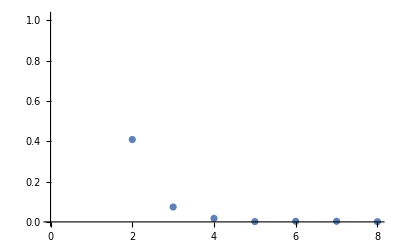

```mathematica
ListPlot[list]
```

```mathematica
a={2.044260666936157,0.4083885339390674,0.07392781686764312,0.017603580674241583,0.0015418038908989657,0.0030197791612239303}
```

{2.04426,0.408389,0.0739278,0.0176036,0.0015418,0.00301978}

```mathematica
Total[a]
```

2.54874

```mathematica
N[Eminusone[-1]]
```

2.04426

```mathematica
N[Eminusone[6]]
```

-0.00099505